# UpSetChart Tests

```mathematica
Quit[];
```

```mathematica
$Path=Prepend[$Path,NotebookDirectory[]];
<<UpSetChart`
```

```mathematica
<<UpSetChart`TestData`
sets=DummyData[1]
```

<|a→{7,77,53,95,42,41},b→{51,88,87,67,90,37,96},c→{15,87,99,6,20,87,98,68},d→{46,85,6,90},e→{72,97,15,55,87}|>

## The Packages of UpSetChart

```mathematica
Translate
```

```mathematica
(*<<UpSetChart`*)
```

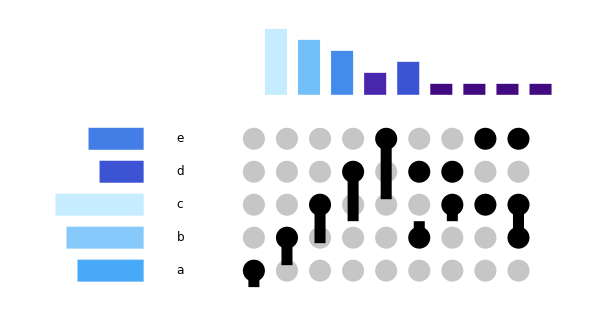

Translate[{Translate[{RGBColor[0.282325, 0.661868, 0.973082],Rectangle[{2,0},{8,2}]},{0,0}],Translate[{RGBColor[0.527193, 0.7932440000000001, 0.9858925000000001],Rectangle[{1,0},{8,2}]},{0,3}],Translate[{RGBColor[0.772061, 0.92462, 0.998703],Rectangle[{0,0},{8,2}]},{0,6}],Translate[{RGBColor[0.235431, 0.32765, 0.833291],Rectangle[{4,0},{8,2}]},{0,9}],Translate[{RGBColor[0.258878, 0.494759, 0.9031865],Rectangle[{3,0},{8,2}]},{0,12}]},{0,0}]

Translate[{Translate[Text[a,{0,0},{-1,0}],{1,1}],Translate[Text[b,{0,0},{-1,0}],{1,4}],Translate[Text[c,{0,0},{-1,0}],{1,7}],Translate[Text[d,{0,0},{-1,0}],{1,10}],Translate[Text[e,{0,0},{-1,0}],{1,13}]},{0,0}]

```mathematica
UpSetChart[sets]
UpSetChart[sets][[1]][[1]]
<<UpSetChart`Calculations`
<<UpSetChart`Graphics`SetsLabels`
calc=CalcThenSortAndFilter[sets];
SetsLabels[ Keys[calc["sets"]]]
```

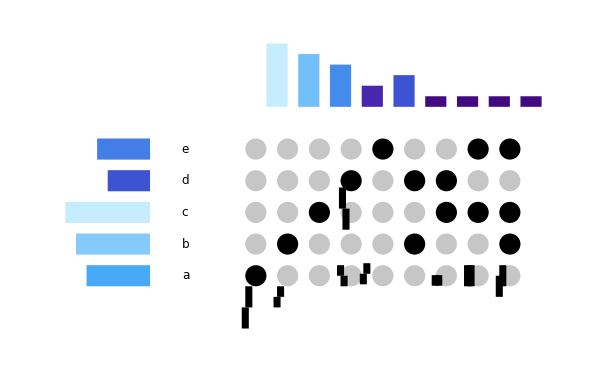

Translate[{Translate[{RGBColor[0.282325, 0.661868, 0.973082],Rectangle[{2,0},{8,2}]},{0,0}],Translate[{RGBColor[0.527193, 0.7932440000000001, 0.9858925000000001],Rectangle[{1,0},{8,2}]},{0,3}],Translate[{RGBColor[0.772061, 0.92462, 0.998703],Rectangle[{0,0},{8,2}]},{0,6}],Translate[{RGBColor[0.235431, 0.32765, 0.833291],Rectangle[{4,0},{8,2}]},{0,9}],Translate[{RGBColor[0.258878, 0.494759, 0.9031865],Rectangle[{3,0},{8,2}]},{0,12}]},{0,0}]

Translate[{Translate[Text[a,{0,0},{-1,0}],{1,1}],Translate[Text[b,{0,0},{-1,0}],{1,4}],Translate[Text[c,{0,0},{-1,0}],{1,7}],Translate[Text[d,{0,0},{-1,0}],{1,10}],Translate[Text[e,{0,0},{-1,0}],{1,13}]},{0,0}]

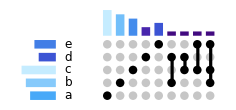
```mathematica
-Graphics-//Rasterize
```

-Graphics-

```mathematica
MatchQ[UpSetChart[sets],UpSetChart[UpSetChart`Utilities`EnsureLabeledSets[sets]]]
```

False

```mathematica
Graphics[
{Text["e"]}
]
```

```mathematica
ImageDimensions[ImageCrop[Graphics[{Text["e"],Text["dasdadas"]}]]][[1]]
```

43

## Unique Intersections

```mathematica
(* Calculates the unique elements for the comparisons *)
<<UpSetChart`UniqueIntersections`
```

```mathematica
UniqueIntersections[sets]
```

<|sets→<|a→{7,77,53,95,42,41},b→{51,88,87,67,90,37,96},c→{15,87,99,6,20,98,68},d→{46,85,6,90},e→{72,97,15,55,87}|>,setNames→{a,b,c,d,e},comparisons→{{},{a},{b},{c},{d},{e},{a,b},{a,c},{a,d},{a,e},{b,c},{b,d},{b,e},{c,d},{c,e},{d,e},{a,b,c},{a,b,d},{a,b,e},{a,c,d},{a,c,e},{a,d,e},{b,c,d},{b,c,e},{b,d,e},{c,d,e},{a,b,c,d},{a,b,c,e},{a,b,d,e},{a,c,d,e},{b,c,d,e},{a,b,c,d,e}},numberOfSets→5,elementsUniqueToComparisons→<|{}→{},{a,b,c,d,e}→{},{a,b,c,d}→{},{a,b,c,e}→{},{a,b,d,e}→{},{a,c,d,e}→{},{b,c,d,e}→{},{a,b,c}→{},{a,b,d}→{},{a,b,e}→{},{a,c,d}→{},{a,c,e}→{},{a,d,e}→{},{b,c,d}→{},{b,c,e}→{87},{b,d,e}→{},{c,d,e}→{},{a,b}→{},{a,c}→{},{a,d}→{},{a,e}→{},{b,c}→{},{b,d}→{90},{b,e}→{},{c,d}→{6},{c,e}→{15},{d,e}→{},{a}→{7,41,42,53,77,95},{b}→{37,51,67,88,96},{c}→{20,68,98,99},{d}→{46,85},{e}→{55,72,97}|>|>

## Utilities

Utilities contains several conditional checkers and helpers.

```mathematica
(* Conditionals for types & passing down options *)
<<UpSetChart`Utilities`
```

```mathematica
EnsureLabeledSets[{{1,2,3},{2,3,4,4,4}}]
```

<|a→{1,2,3},b→{2,3,4}|>

```mathematica
ListOfListsQ[sets]
LabeledSetsQ[sets]
```

ListOfListsQ[<|a→{7,77,53,95,42,41},b→{51,88,87,67,90,37,96},c→{15,87,99,6,20,87,98,68},d→{46,85,6,90},e→{72,97,15,55,87}|>]

True

## Calculations

While Unique Intersections does all the calculations we need for this chart, the chart may want us to sort and filter results as well.
This “super” function does this.

```mathematica
(* Calls UniqueIntersections and sorts & filters data *)
<<UpSetChart`Calculations`
```

```mathematica
calc=CalcThenSortAndFilter[sets]
```

<|sets→<|a→{7,77,53,95,42,41},b→{51,88,87,67,90,37,96},c→{15,87,99,6,20,87,98,68},d→{46,85,6,90},e→{72,97,15,55,87}|>,comparisons→<|{a}→{7,41,42,53,77,95},{b}→{37,51,67,88,96},{c}→{20,68,98,99},{d}→{46,85},{e}→{55,72,97},{b,d}→{90},{c,d}→{6},{c,e}→{15},{b,c,e}→{87}|>|>

### Calculation Utilities

```mathematica
(* Sort & filter functions *)
<<UpSetChart`Calculations`Utilities`
```

## Graphics

```mathematica
(* Returns the graphics for UpSetChart *)
<<UpSetChart`Graphics`
```

Graphics is a wrapper GraphicComponents returning the Graphic Item. Allows for processing of the Options before passing them

```mathematica
UpSetGraphics[
	calc["sets"], 
	calc["comparisons"],
	"ColorGradient"->"AvocadoColors",
	"ComponentSpacing"->{1,1},
	"IndicatorRadius"->1,
	"IndicatorSpacing"->{1,1}
]
```

UpSetGraphics[<|a→{7,77,53,95,42,41},b→{51,88,87,67,90,37,96},c→{15,87,99,6,20,87,98,68},d→{46,85,6,90},e→{72,97,15,55,87}|>,<|{a}→{7,41,42,53,77,95},{b}→{37,51,67,88,96},{c}→{20,68,98,99},{d}→{46,85},{e}→{55,72,97},{b,d}→{90},{c,d}→{6},{c,e}→{15},{b,c,e}→{87}|>,ColorGradient→AvocadoColors,ComponentSpacing→{1,1},IndicatorRadius→1,IndicatorSpacing→{1,1}]

### Utilities

Graphic Utilities is a wrapper over the four main components and returns them as a list.

```mathematica
(* Returns each components for the UpSetChart *)
<<UpSetChart`Graphics`Utilities`
```

```mathematica
gc=GraphicComponents[calc["sets"], calc["comparisons"],"IndicatorRadius"->1]
```

{{{RGBColor[0.282325, 0.661868, 0.973082],Rectangle[{2,2},{8,4}]},{RGBColor[0.527193, 0.7932440000000001, 0.9858925000000001],Rectangle[{1,5},{8,7}]},{RGBColor[0.772061, 0.92462, 0.998703],Rectangle[{0,8},{8,10}]},{RGBColor[0.235431, 0.32765, 0.833291],Rectangle[{4,11},{8,13}]},{RGBColor[0.258878, 0.494759, 0.9031865],Rectangle[{3,14},{8,16}]}},{{RGBColor[0.772061, 0.92462, 0.998703],Rectangle[{19,17},{21,23}]},{RGBColor[0.4455703333333333, 0.749452, 0.9816223333333334],Rectangle[{22,17},{24,22}]},{RGBColor[0.26669366666666666, 0.550462, 0.926485],Rectangle[{25,17},{27,21}]},{RGBColor[0.28235299999999997, 0.1497248, 0.6790623333333333],Rectangle[{28,17},{30,19}]},{RGBColor[0.235431, 0.32765, 0.833291],Rectangle[{31,17},{33,20}]},{RGBColor[0.25984599999999997, 0.040508133333333335, 0.5018556666666667],Rectangle[{34,17},{36,18}]},{RGBColor[0.25984599999999997, 0.040508133333333335, 0.5018556666666667],Rectangle[{37,17},{39,18}]},{RGBColor[0.25984599999999997, 0.040508133333333335, 0.5018556666666667],Rectangle[{40,17},{42,18}]},{RGBColor[0.25984599999999997, 0.040508133333333335, 0.5018556666666667],Rectangle[{43,17},{45,18}]}},{Text[a,{10,3},{-1,0}],Text[b,{10,6},{-1,0}],Text[c,{10,9},{-1,0}],Text[d,{10,12},{-1,0}],Text[e,{10,15},{-1,0}]},{{{{GrayLevel[0],Disk[{20,3},1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{23,3},1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{26,3},1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{29,3},1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{32,3},1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{35,3},1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{38,3},1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{41,3},1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{44,3},1]}},{{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{20,6},1]},{GrayLevel[0],Disk[{23,6},1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{26,6},1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{29,6},1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{32,6},1]},{GrayLevel[0],Disk[{35,6},1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{38,6},1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{41,6},1]},{GrayLevel[0],Disk[{44,6},1]}},{{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{20,9},1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{23,9},1]},{GrayLevel[0],Disk[{26,9},1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{29,9},1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{32,9},1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{35,9},1]},{GrayLevel[0],Disk[{38,9},1]},{GrayLevel[0],Disk[{41,9},1]},{GrayLevel[0],Disk[{44,9},1]}},{{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{20,12},1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{23,12},1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{26,12},1]},{GrayLevel[0],Disk[{29,12},1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{32,12},1]},{GrayLevel[0],Disk[{35,12},1]},{GrayLevel[0],Disk[{38,12},1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{41,12},1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{44,12},1]}},{{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{20,15},1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{23,15},1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{26,15},1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{29,15},1]},{GrayLevel[0],Disk[{32,15},1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{35,15},1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{38,15},1]},{GrayLevel[0],Disk[{41,15},1]},{GrayLevel[0],Disk[{44,15},1]}}},{{GrayLevel[0],Rectangle[{59/3,3},{62/3,3}]},{GrayLevel[0],Rectangle[{68/3,6},{71/3,6}]},{GrayLevel[0],Rectangle[{77/3,9},{80/3,9}]},{GrayLevel[0],Rectangle[{86/3,12},{89/3,12}]},{GrayLevel[0],Rectangle[{95/3,15},{98/3,15}]},{GrayLevel[0],Rectangle[{104/3,6},{107/3,12}]},{GrayLevel[0],Rectangle[{113/3,9},{116/3,12}]},{GrayLevel[0],Rectangle[{122/3,9},{125/3,15}]},{GrayLevel[0],Rectangle[{131/3,6},{134/3,15}]}}}}

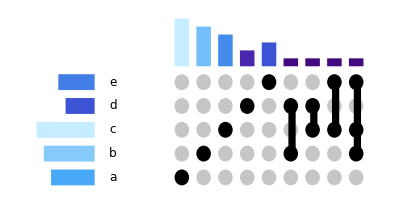

```mathematica
Graphics[{gc,
Inset[
Graphics[
Axes->{True,False},
AxesOrigin->{0,0},
ImagePadding->None,
ImageMargins->0
],
{0,0},{0,0},{}
]

}]
```

```mathematica
sbc = gc[[1]];cbc = gc[[2]];cbl = gc[[3]];ig = gc[[4]];
```

```mathematica
PacletInstall["GraphicsInformation","Site"->"http://raw.githubusercontent.com/carlwoll/GraphicsInformation/master"];
```

```mathematica
<<GraphicsInformation`
```

```mathematica
I
```

### Comparisons Bar Chart

Comparisons Bar Chart produces the bar chart for the cardinality of the set comparisons

```mathematica
(* Components for charts *)
<<UpSetChart`Graphics`ComparisonsBarChart`
```

```mathematica
ComparisonsBarChart[calc["comparisons"],
 Max[Length/@calc["comparisons"]], Keys@calc["sets"]
]//Graphics[#,ImageSize->Tiny]&
```

Keys::invrl: The argument CalcThenSortAndFilter[sets][sets] is not a valid Association or a list of rules.

-Graphics-

### Grid Indicator

Grid Indicator produces the bubble heatmap which indicates which sets correspond to which comparisons

```mathematica
<<UpSetChart`Graphics`IndicatorGrid`
```

Get::noopen: Cannot open UpSetChart`Graphics`IndicatorGrid`.

$Failed

```mathematica
IndicatorGrid[Keys[calc["sets"]],Keys[calc["comparisons"]]]//Graphics[#,ImageSize->Tiny]&
IndicatorGrid[Keys[calc["sets"]],Keys[calc["comparisons"]]]
```

Keys::invrl: The argument calc[sets] is not a valid Association or a list of rules.

Keys::invrl: The argument calc[comparisons] is not a valid Association or a list of rules.

-Graphics-

Keys::invrl: The argument calc[sets] is not a valid Association or a list of rules.

Keys::invrl: The argument calc[comparisons] is not a valid Association or a list of rules.

IndicatorGrid[Keys[calc[sets]],Keys[calc[comparisons]]]

### Sets Bar Chart

Produces the Bar Chart for the cardinality of sets

```mathematica
<<UpSetChart`Graphics`SetsBarChart`
```

```mathematica
SetsBarChart[calc["sets"], Keys[calc["sets"]], Max[Length/@calc["sets"]]]//Graphics[#,ImageSize->Tiny]&
```

Keys::invrl: The argument CalcThenSortAndFilter[sets][sets] is not a valid Association or a list of rules.

-Graphics-

### Labels

Produces the labels of the sets. Works best with short labels

```mathematica
<<UpSetChart`Graphics`SetsLabels`
```

```mathematica
SetsLabels[ Keys[calc["sets"]]]//Graphics[#,ImageSize->Tiny]&
```

-Graphics-

```mathematica
SetsLabels[ Keys[calc["sets"]]]
```

Translate[{Translate[Text[a,{0,0},{-1,0}],{1,3}],Translate[Text[b,{0,0},{-1,0}],{1,6}],Translate[Text[c,{0,0},{-1,0}],{1,9}],Translate[Text[d,{0,0},{-1,0}],{1,12}],Translate[Text[e,{0,0},{-1,0}],{1,15}]},{0,0}]